Add the nonlinear directory to our paths, so we can import data easily

```mathematica
AppendTo[$Path, ToFileName[{$HomeDirectory,"My Documents\Matlab\Nonlinear"}]];
```

{a→0.338415,b→0.0507534,w→5.61535,phi→-0.550549}

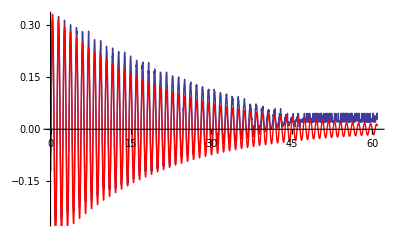

```mathematica
data=Import["firstrun.txt","CSV"];
gd=ListLinePlot[data];

myfit=a*Sin[w t+phi]*Exp[-b t];
fitparams=FindFit[data,myfit,{a,b,w,phi},t]

newfit=myfit/.fitparams;
time=Transpose[data][[1]];
theory =Transpose[{time,newfit/.t->time}];
gt = ListLinePlot[theory,PlotStyle->Red];

Show[gd,gt]
```

Get the effective length of our pendlum:

```mathematica
9.8/(w/.fitparams)^2
```

0.310794

## Driven Damped SHO

```mathematica
drive=Import["driven1_drive.txt","CSV"];
response=Import["driven1_response.txt","CSV"];
time=Transpose[drive][[1]];
(* Plot the data *)
gdd=ListLinePlot[drive];
gdr=ListLinePlot[response];
```

```mathematica
myfit=a*Sin[w t+phi];
fitparamsDrive=FindFit[drive,{myfit,{w>1}},{a,w,phi},t,Method->NMinimize]
fitparamsResponse=FindFit[response,{myfit,{w>1}},{a,w,phi},t,Method->NMinimize]
```

{a→-0.172278,w→10.5103,phi→-3.44616}

{a→0.38593,w→10.5034,phi→-6.77425}

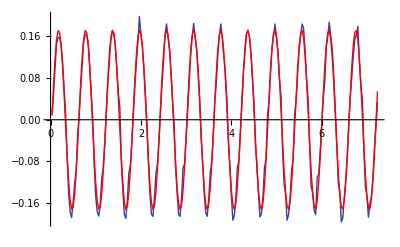

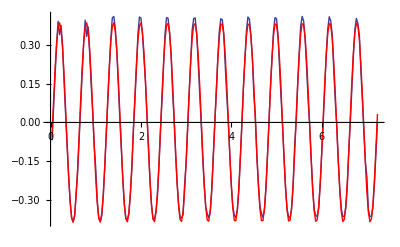

```mathematica
(* Evaluate and Plot the fit *)
newfitDrive=myfit/.fitparamsDrive;
fitDrive =Transpose[{time,newfitDrive/.t->time}];
newfitResponse=myfit/.fitparamsResponse;
fitResponse=Transpose[{time,newfitResponse/.t->time}];
gtd = ListLinePlot[fitDrive,PlotStyle->Red];
gtr = ListLinePlot[fitResponse,PlotStyle->Red];

Show[gdd,gtd]
Show[gdr,gtr]
```